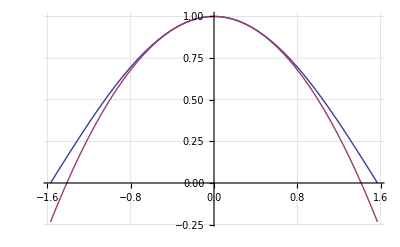

```mathematica
Plot[{Cos[x],1-(1/2)x^2},{x,-π/2,π/2},GridLines->Automatic]
```

```mathematica
p:=Integrate[#1 #2,{x,-π/2,π/2}]&;
```

```mathematica
Sqrt[N[p[Cos[x]-(1-(1/2)x^2),Cos[x]-(1-(1/2)x^2)]]]
```

0.140165

```mathematica
{p1[x_],p2[x_]}=Orthogonalize[{1,x^2},p];
```

```mathematica
p[Cos[x],p1[x]]p1[x]+p[Cos[x],p2[x]]p2[x]
```

2/π+(60 (-12+π^2) (-π^2/12+x^2))/π^5

```mathematica
{p[%,Cos[x]-%],Sqrt[N[p[Cos[x]-%,Cos[x]-%]]],Simplify[N[%]]}
```

{0,0.0305989,0.980162-0.417698 x^2}

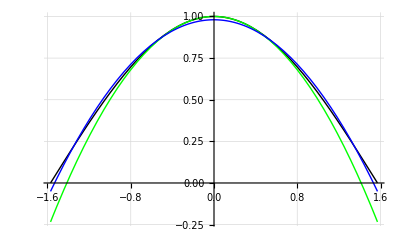

```mathematica
Plot[{Cos[x],1-(1/2)x^2,%%},{x,-π/2,π/2},GridLines->Automatic,PlotStyle->{Black,Green,Blue}]
```

```mathematica
Graphics3D[{Arrow[{{{6,1,0},{4,2,3}},{{6,1,0},{4,2,0}},{{0,-1,0},{6,1,0}},{{0,-1,0},{4,2,0}},{{0,-1,0},{4,2,3}},{{4,2,0},{4,2,3}}}],Line[{{-1,-3,0},{7,-3,0},{7,5,0},{-1,5,0},{-1,-3,0}}]},Boxed->False]
```

-Graphics3D-